```mathematica
fixedPoints=Solve[{r*x+y-x==0,-x+r*y-y^3-y==0},{x,y}];
fixedPointsY=y/. fixedPoints;

bifurcationPlot=ParametricPlot[Evaluate[{r,#}&/@fixedPointsY],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","y"},PlotLabel->"Bifurcation Plot",PlotStyle->{Red,Blue,Green},Frame->True];
```

```mathematica
"bifurcation_plot.png"
```

bifurcation_plot.png

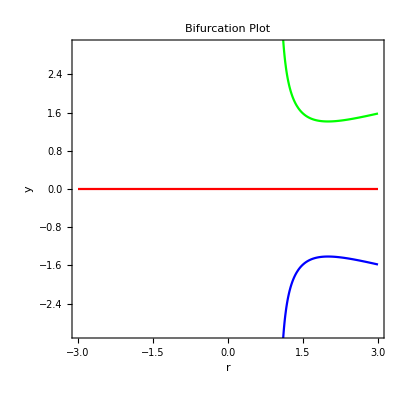

```mathematica
fixedPoints=Solve[{r*x+y-x==0,-x+r*y-y^3-y==0},{x,y}];
fixedPointsY=y/. fixedPoints;

bifurcationPlot=ParametricPlot[Evaluate[{r,#}&/@fixedPointsY],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","y"},PlotLabel->"Bifurcation Plot",PlotStyle->{Red,Blue,Green},Frame->True];

bifurcationPlot
```

```mathematica
-Graphics-f<<ff<ff<f<cf<ffffffffffffvfvffff<f<fc
```

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Find the fixed points*)
fixedPoints=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];
fixedPointsY=y/. fixedPoints;

(*Bifurcation plot*)
bifurcationPlot=ParametricPlot[Evaluate[{r,#}&/@fixedPointsY],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","y"},PlotLabel->"Bifurcation Plot",Frame->True];

(*Stability analysis*)
stability=Table[Eigenvalues[jacobianMatrix/. fixedPoints[[i]]],{i,Length[fixedPoints]}];

stableUnstable=Table[If[And@@Negative[Re[stability[[i]]]],"Stable","Unstable"],{i,Length[fixedPoints]}];

Show[bifurcationPlot,Graphics[{Text[stableUnstable[[1]],{-2,fixedPointsY[[1]]/. r->-2}],Text[stableUnstable[[2]],{-2,fixedPointsY[[2]]/. r->-2}],Text[stableUnstable[[3]],{-2,fixedPointsY[[3]]/. r->-2}]}]]
```

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Find the fixed points*)
fixedPoints=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];
fixedPointsY=y/. fixedPoints;

(*Calculate eigenvalues of the Jacobian matrix at fixed points*)
eigenvalues=Table[Eigenvalues[jacobianMatrix/. fixedPoints[[i]]],{i,Length[fixedPoints]}];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
eigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[eigenvalues[[i,j]]]}&/@{1,2},{i,Length[fixedPoints]}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Re(λ)"},PlotLabel->"Eigenvalues Plot",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

eigenvaluePlot
```

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Find the fixed points*)
fixedPoints=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Calculate eigenvalues of the Jacobian matrix at fixed points*)
eigenvalues=Table[Eigenvalues[jacobianMatrix/. fixedPoints[[i]]],{i,Length[fixedPoints]}];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
eigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[eigenvalues[[i,j]]]}/. fixedPoints[[i]],{i,Length[fixedPoints]},{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Re(λ)"},PlotLabel->"Eigenvalues Plot",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

eigenvaluePlot
```

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Find the fixed points*)
fixedPoints=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Calculate eigenvalues of the Jacobian matrix at fixed points*)
eigenvalues=Table[Eigenvalues[jacobianMatrix/. fixedPoints[[i]]],{i,Length[fixedPoints]}];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
eigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[eigenvalues[[i,j]]]}/. fixedPoints[[i]],{i,Length[fixedPoints]},{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Re(λ)"},PlotLabel->"Eigenvalues Plot",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

eigenvaluePlot
```

-Graphics-

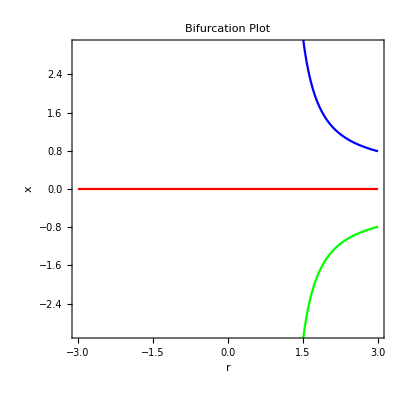

```mathematica
fixedPoints=Solve[{r*x+y-x==0,-x+r*y-y^3-y==0},{x,y}];
fixedPointsX=x/. fixedPoints;

bifurcationPlotX=ParametricPlot[Evaluate[{r,#}&/@fixedPointsX],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","x"},PlotLabel->"Bifurcation Plot",PlotStyle->{Red,Blue,Green},Frame->True];

bifurcationPlotX
```

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Find the fixed points*)
fixedPoints=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Calculate eigenvalues of the Jacobian matrix at fixed points*)
eigenvalues=Table[Eigenvalues[jacobianMatrix/. fixedPoints[[i]]],{i,Length[fixedPoints]}];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[eigenvalues[[i,j]]]}/. fixedPoints[[i]],{i,Length[fixedPoints]},{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Re(λ)"},PlotLabel->"Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

(*Parametric plot of the imaginary part of the eigenvalues as a function of r*)
imagEigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Im[eigenvalues[[i,j]]]}/. fixedPoints[[i]],{i,Length[fixedPoints]},{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Im(λ)"},PlotLabel->"Imaginary Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

(*Display both plots*)
GraphicsGrid[{{realEigenvaluePlot},{imagEigenvaluePlot}}]
```

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Define a function to get the fixed points*)
fixedPoints[r_]:=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Define a function to get the eigenvalues*)
eigenvalues[r_]:=Eigenvalues[jacobianMatrix/. fixedPoints[r]];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[#[[j]]]}&/@eigenvalues[r],{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Re(λ)"},PlotLabel->"Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

(*Parametric plot of the imaginary part of the eigenvalues as a function of r*)
imagEigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Im[#[[j]]]}&/@eigenvalues[r],{j,1,2}]],{r,-3,3},PlotRange->{-3,3},AxesLabel->{"r","Im(λ)"},PlotLabel->"Imaginary Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

(*Display both plots*)
GraphicsGrid[{{realEigenvaluePlot},{imagEigenvaluePlot}}]
```

SetDelayed::write: Tag List in {{x→0,y→0},{x→(√(2-2 r+r^2))/(-1+r)^(3/2),y→-(√(2-2 r+r^2))/(√(-1+r))},{x→-(√(2-2 r+r^2))/(-1+r)^(3/2),y→(√(2-2 r+r^2))/(√(-1+r))}}[r_] is Protected.

SetDelayed::write: Tag List in {{(-1-ⅈ)+r,(-1+ⅈ)+r},{(-4+2 r-r^2-√(32+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))/(2 (-1+r)),(-4+2 r-r^2+√(32-64 r+«1»-36 Power[«2»]+9 Power[«2»]))/(2 (-1+r))},{(-4+2 r-r^2-√(32+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))/(2 (-1+r)),(-4+2 r-r^2+√(32-64 r+68 Power[«2»]-36 Power[«2»]+9 Power[«2»]))/(2 (-1+r))}}[r_] is Protected.

Part::partd: Part specification r⟦1⟧ is longer than depth of object.

Part::partd: Part specification r⟦2⟧ is longer than depth of object.

Part::partd: Part specification (-2.99988)⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification r⟦1⟧ is longer than depth of object.

Part::partd: Part specification r⟦2⟧ is longer than depth of object.

Part::partd: Part specification (-2.99988)⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Define a function to get the fixed points*)
fixedPoints[r_]:=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Define a function to get the eigenvalues*)
eigenvalues[r_]:=Eigenvalues[jacobianMatrix/. fixedPoints[r]];

(*Parametric plot of the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=ParametricPlot[Evaluate[Table[{r,Re[#[[j]]]}&/@eigenvalues[r],{j,1,2}]],{r,-3,3},PlotRange->All,AxesLabel->{"r","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

realEigenvaluePlot
```

Eigenvalues::matsq: Argument {{{-1+r,1},{-1,-1+r}},{{-1+r,1},{-1,-1+r-(3 (2-2 r+r^2))/(-1+r)}},{{-1+r,1},{-1,-1+r-(3 (2-2 r+r^2))/(-1+r)}}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument -2.99988 at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

-Graphics-

```mathematica
r=1;
streamPlot=StreamPlot[{r*x+y,-x+r*y-y^3},{x,-3,3},{y,-3,3},StreamStyle->{Orange,Thick},VectorStyle->Arrowheads[0.02],StreamPoints->Fine,Mesh->All,Axes->True,AxesLabel->{x,y},PlotLabel->"Customized StreamPlot"];

legend=LineLegend[{Orange},{"Vector Field"},LabelStyle->{FontFamily->"Arial",FontSize->12},LegendMarkerSize->{30,1},LegendFunction->"Panel"];

Show[streamPlot,Graphics[Inset[legend,Scaled[{0.8,0.85}]]]]
```

-Graphics-

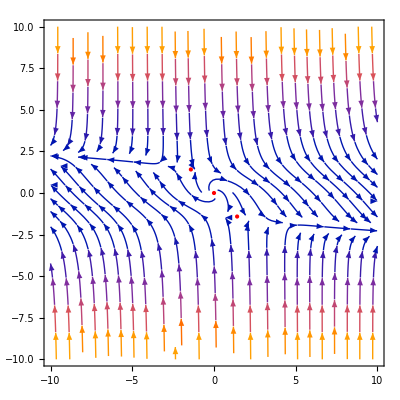

```mathematica
r=1;
fixedPoints=Solve[{r*x+y==0,-x+r*y-y^3==0},{x,y}];
fixedPointsCoordinates={x,y}/. fixedPoints;

streamPlot=StreamPlot[{r*x+y,-x+r*y-y^3},{x,-10,10},{y,-10,10},VectorStyle->Arrowheads[0.02]];

fixedPointDots=Graphics[{PointSize[Large],Red,Point[fixedPointsCoordinates]}];

Show[streamPlot,fixedPointDots]
```

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Define a function to get the fixed points*)
fixedPoints[r_]:=Solve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Define a function to get the eigenvalues*)
eigenvalues[r_]:=Eigenvalues[jacobianMatrix/. fixedPoints[r]];

(*Define a function to extract the real parts of the eigenvalues*)
realEigenvalues[r_]:=Re/@Flatten[eigenvalues[r]];

(*Plot the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=Plot[Evaluate[realEigenvalues[r]],{r,-3,3},PlotRange->All,AxesLabel->{"r","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

realEigenvaluePlot
```

SetDelayed::write: Tag List in {{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[r_] is Protected.

ReplaceAll::reps: {{{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[r]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[-2.99988]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0.,y→0.},{x→1.41421,y→-1.41421},{x→-1.41421,y→1.41421}}[-2.99988]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[x,y,r]

(*Define the system of equations*)
f[x_,y_,r_]:=r*x+y-x
g[x_,y_,r_]:=-x+r*y-y^3-y

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[{f[x,y,r],g[x,y,r]},{{x,y}}];

(*Define a function to get the fixed points numerically*)
fixedPoints[r_?NumericQ]:=NSolve[{f[x,y,r]==0,g[x,y,r]==0},{x,y}];

(*Define a function to get the eigenvalues*)
eigenvalues[r_?NumericQ]:=Eigenvalues[jacobianMatrix/. fixedPoints[r]];

(*Extract the real parts of the eigenvalues for each r value*)
realEigenvalues=Table[{r,Re/@eigenvalues[r]},{r,-3,3,0.01}];

(*Plot the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=ListLinePlot[realEigenvalues,PlotRange->All,AxesLabel->{"r","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue,Green,Orange,Magenta,Cyan}];

realEigenvaluePlot
```

SetDelayed::write: Tag List in {{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[r_?NumericQ] is Protected.

ReplaceAll::reps: {{{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[-3.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[-2.99]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0,y→0},{x→√2,y→-√2},{x→-√2,y→√2}}[-2.98]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {{{x→0,y→0},{x→1.414213562373095,y→-1.414213562373095},{x→-1.414213562373095,y→1.414213562373095}}[-3.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0,y→0},{x→1.414213562373095,y→-1.414213562373095},{x→-1.414213562373095,y→1.414213562373095}}[-2.99]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x→0,y→0},{x→1.414213562373095,y→-1.414213562373095},{x→-1.414213562373095,y→1.414213562373095}}[-2.98]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[y,r]

(*Define the eigenvalues*)
lambda1[y_,r_]:=r-Sqrt[y^4-1]-y^2
lambda2[y_,r_]:=r+Sqrt[y^4-1]-y^2

(*Plot the real part of the eigenvalues as a function of y*)
realEigenvaluePlot=Plot[Evaluate[{Re[lambda1[y,r]],Re[lambda2[y,r]]}],{y,-3,3},PlotRange->All,AxesLabel->{"y","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(λ\), \(1\)]\)","\!\(\*SubscriptBox[\(λ\), \(2\)]\)"}];

realEigenvaluePlot
```

-Graphics-

C:\Users\Petrb\Desktop\RUC\6 th semester\Dynamical Systems\Homeworks\3rd_handin\Dynamical Systems\imagesrealEigenvaluePlot_300dpi.png

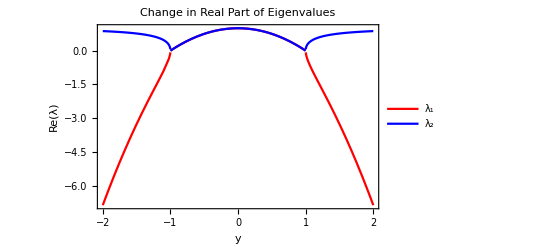

```mathematica
Clear[y,r]

(*Define the eigenvalues*)
lambda1[y_,r_]:=r-Sqrt[y^4-1]-y^2
lambda2[y_,r_]:=r+Sqrt[y^4-1]-y^2

(*Set r to 1*)
r=1;

(*Plot the real part of the eigenvalues as a function of y*)
realEigenvaluePlot=Plot[Evaluate[{Re[lambda1[y,r]],Re[lambda2[y,r]]}],{y,-2,2},PlotRange->All,AxesLabel->{"y","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(λ\), \(1\)]\)","\!\(\*SubscriptBox[\(λ\), \(2\)]\)"}];
filePath="C:\\Users\\Petrb\\Desktop\\RUC\\6 th semester\\Dynamical Systems\\Homeworks\\3rd_handin\\Dynamical Systems\\imagesrealEigenvaluePlot_300dpi.png"
realEigenvaluePlot
```

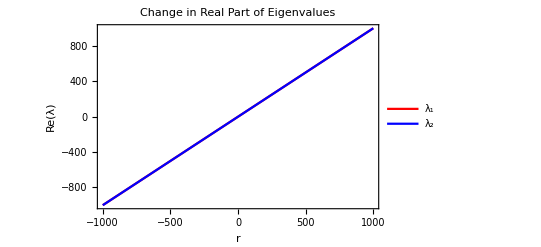

realEigenvaluePlot_300dpi.png

```mathematica
Clear[r,y]

(*Define the eigenvalues*)
lambda1[y_,r_]:=r-Sqrt[y^4-1]-y^2
lambda2[y_,r_]:=r+Sqrt[y^4-1]-y^2

(*Set y to 1*)
y=0;

(*Plot the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=Plot[Evaluate[{Re[lambda1[y,r]],Re[lambda2[y,r]]}],{r,-1000,1000},PlotRange->All,AxesLabel->{"r","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(λ\), \(1\)]\)","\!\(\*SubscriptBox[\(λ\), \(2\)]\)"}];

realEigenvaluePlot
Export["realEigenvaluePlot_300dpi.png",realEigenvaluePlot,ImageResolution->300]
```

```mathematica
"realEigenvaluePlot_300dpi.png"
```

realEigenvaluePlot_300dpi.png

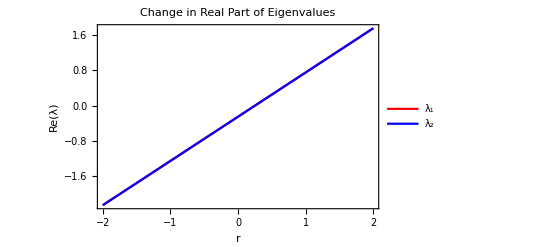

```mathematica
Clear[r,y]

(*Define the eigenvalues*)
lambda1[y_,r_]:=r-Sqrt[y^4-1]-y^2
lambda2[y_,r_]:=r+Sqrt[y^4-1]-y^2

(*Set y to 0.5*)
y=0.5;

(*Plot the real part of the eigenvalues as a function of r*)
realEigenvaluePlot=Plot[Evaluate[{Re[lambda1[y,r]],Re[lambda2[y,r]]}],{r,-2,2},PlotRange->All,AxesLabel->{"r","Re(λ)"},PlotLabel->"Change in Real Part of Eigenvalues",Frame->True,PlotStyle->{Red,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(λ\), \(1\)]\)","\!\(\*SubscriptBox[\(λ\), \(2\)]\)"}];

realEigenvaluePlot
```